ЛР2 (Бусько Егор, 3 вариант)

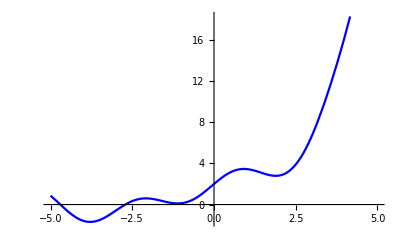

```mathematica
Clear["Global`*"];
f[x_]:= 2^x+Cos[x]+Sin[2*x];
Plot[f[x], {x, -5,5},PlotStyle->Blue]
x[0]=3.4;
x[1]=3.6;
x[2]=3.8;
x[3]=3.10;
t=3.9;
vectX={x[0],x[1],x[2], x[3]};
```

## task 1

```mathematica
Lagrange[t_]:=Sum[f[x[j]]*Product[If[i==j,1,(t-x[i])/(x[j]-x[i])],{i,0,Length[vectX]-1}],{j,0,Length[vectX]-1}];
```

```mathematica
Print["f(3.9) = ", f[t]];
Print["L(3.9) = ", Lagrange[t]];
Print["InterpolatingPolynomial(3.9) = ",InterpolatingPolynomial[{{x[0], f[x[0]]},{x[1], f[x[1]]}, {x[2], f[x[2]]}, {x[3], f[x[3]]}},x]/.x->t];
```

f(3.9) = 15.2011

L(3.9) = 15.1944

InterpolatingPolynomial(3.9) = 15.1944

```mathematica
Print["f''(3.9) = ",D[f[x],{x,2}]/.x->t];
Print["p''(3.9) with Lagrange = ",D[Lagrange[x],{x,2}]/.x->t];
Print["p''(3.9) with InterpolatingPolynomial = ",D[InterpolatingPolynomial[{{x[0], f[x[0]]},{x[1], f[x[1]]}, {x[2], f[x[2]]}, {x[3], f[x[3]]}},x],{x,2}]/.x->t];
```

f''(3.9) = 3.90422

p''(3.9) with Lagrange = 2.7778

p''(3.9) with InterpolatingPolynomial = 2.7778

## task 2

```mathematica
Pade[f_,{x_,x0_,{m_,n_}}]:=Module[{table=Table[0,0], i=1,sum = 0, count = 0,series=Series[f[x],{x,x0,m+n}], z, Res =0},
For[i,i≤m+n+1, i++,
sum = SeriesCoefficient[series, i-1]+Sum[SeriesCoefficient[series, i-k-1] q[k],{k, 1, i-1}];
AppendTo[table,sum==p[i-1]];
];
z=Join[Array[p[#]->0&,n,{m+1, m+n}], Array[q[#]->0&,m , {n+1, m+n}]];
table=table/.z;
solution=NSolve[table, Join[Array[p[#]&,m+1,{0,m}], Array[q[#]&, n, {1, n}]]];
Res = Sum[p[k] (x-x0)^(k), {k, 0,m}]/ (1+Sum[q[k] (x-x0)^(k), {k, 1,n}])/.solution;
Return[Res[[1]]];
];
```

(15.2011+9.40315 (-3.9+x)+2.65371 (-3.9+x)^2+1.6005 (-3.9+x)^3+0.763353 (-3.9+x)^4)/(1-0.114478 (-3.9+x)+0.130074 (-3.9+x)^2-0.017598 (-3.9+x)^3)

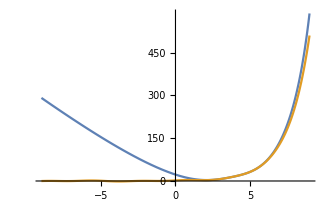

```mathematica
fPade=Pade[f,{x,t,{4,3}}]
Plot[{fPade, f[x]}, {x, -9,9}]
```